## Nuclear charge density

## Using Fermi-distribution for the charge of the nucleus

-Graphics-

### Constants

```mathematica
a=0.54;(*difussenes parameter*)
e=1;
Z=72;
A=163;
```

### Fermi distribution

```mathematica
Fermi[r_,a_]:=1/(1+Exp[r/a]);
```

### Functions

```mathematica
Subscript[R, half][x_]:=1.128 x^(1/3)-0.89 x^(-1/3);
Subscript[ρ, 0]=0.17*e*Z/A;
R[A_]:=1.25*A^(1/3);
ρ[r_,a_]:=Subscript[ρ, 0]*Fermi[r-Subscript[R, half][A],a];
```

## The mean square of the charge distribution

This is also known as the second radial moment of the nuclear charge distribution ⟨r^2⟩

```mathematica
Subscript[RMS, charge][a_,R_]:=Integrate[r^2*ρ[r,a]*4π*r^2,{r,0,R}];
Subscript[RMS, const][A_]:=3/5 R[A]^2;
```

## Barrett Moment for the charge distribution

```mathematica
Subscript[RMS, Barret][a_,α_,k_]:=(4π)/Z Integrate[ρ[r,a]Exp[-α*r] r^(k+2),{r,0,Infinity}];
```

## Plot -Graphics-

```mathematica
t1[diff_]:=Table[{q,Subscript[RMS, charge][diff,q]},{q,0,3,0.25}];
t2[diff_]:=Table[{q,Sqrt[Subscript[RMS, charge][diff,q]]},{q,0,3,0.25}];
l1={{0.,0.},{0.25,0.0001663619350572994},{0.5,0.005280576808420224},{0.75,0.039750807741982225},{1.,0.16594374804109344},{1.25,0.5013332946382637},{1.5,1.2340235243452826},{1.75,2.6363513798972202},{2.,5.07626031475864},{2.25,9.026131362968462},{2.5,15.068765505678781},{2.75,23.90023357134431},{3.,36.32934970029538}};
l2=Table[{l1[[i,1]],Sqrt[l1[[i,2]]]},{i,1,Length[l1]}];
```

```mathematica
chargeplot[diff_]:=ListPlot[{t1[diff],t2[diff]},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotStyle->{{Thick,Red},{Blue,Thick}},PlotMarkers->{Automatic, Medium},LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"R [fm]","2^nd radial moment"},PlotLegends->Placed[{"TraditionalForm`⟩","√TraditionalForm`⟩"},{0.2,0.7}],PlotRange->All,Epilog->Inset[Style[StringTemplate["a_diff=``"][diff],19,Italic,Bold,Black,FontFamily->"Menlo"],Scaled[{0.7,0.75}]],ImageSize->Large];
```

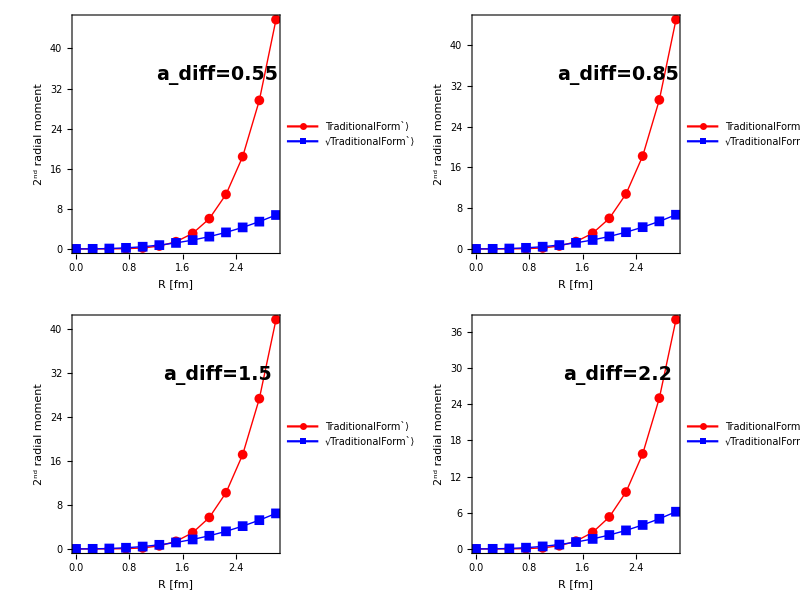

```mathematica
Grid[{{chargeplot[0.55],chargeplot[0.85]},{chargeplot[1.5],chargeplot[2.2]}},Frame->All]
```

## Plot -Graphics-

```mathematica
t1[α_,k_]:=Table[{a,Subscript[RMS, Barret][a,α,k]},{a,0.1,2.5,0.35}];
t2[α_,k_]:=Table[{a,Sqrt[Subscript[RMS, Barret][a,α,k]]},{a,0.1,2.5,0.35}];
```

```mathematica
barretplot[α_,k_]:=ListPlot[{t1[α,k],t2[α,k]},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotStyle->{{Thick,Red},{Blue,Thick}},PlotMarkers->{Automatic, Medium},LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"diffuseness","Barret moment"},PlotLegends->Placed[{"TraditionalForm`⟩","√TraditionalForm`⟩"},{0.2,0.7}],PlotRange->All,Epilog->Inset[Style[StringTemplate["α= ``\nk=``"][0.5,1],19,Italic,Bold,Black,FontFamily->"Menlo"],Scaled[{0.7,0.75}]],ImageSize->Large];
```

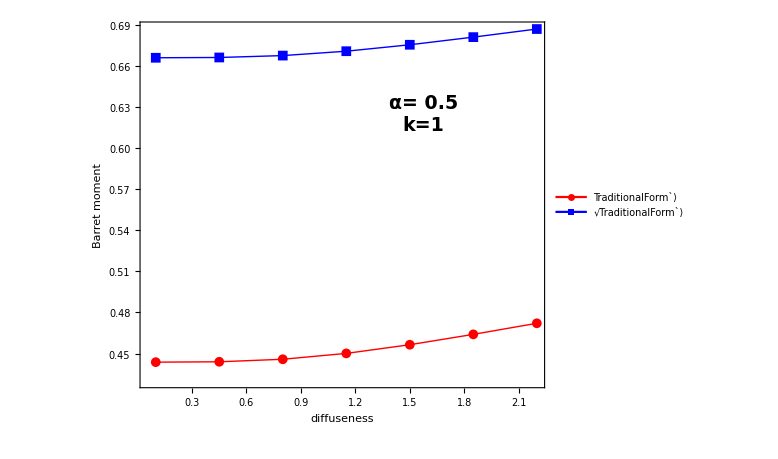

```mathematica
barretplot[0.5,1]
```

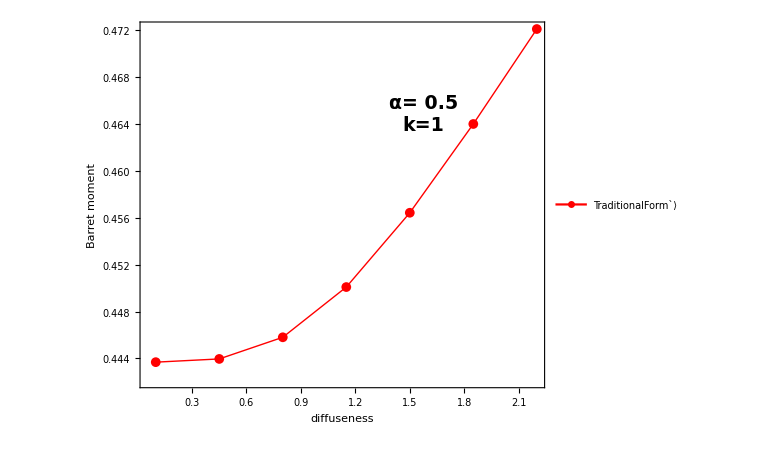

```mathematica
ListPlot[{{0.1,0.44368221502806066},{0.44999999999999996,0.4439575103679902},{0.7999999999999999,0.4458034810585667},{1.15,0.45008652926892584},{1.5,0.4564230105327962},{1.85,0.46399352037265695},{2.1999999999999997,0.4720900865723293}},Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotStyle->{{Thick,Red},{Blue,Thick}},PlotMarkers->{Automatic, Medium},LabelStyle->{20,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"diffuseness","Barret moment"},PlotLegends->Placed[{"TraditionalForm`⟩","√TraditionalForm`⟩"},{0.2,0.7}],PlotRange->All,Epilog->Inset[Style[StringTemplate["α= ``\nk=``"][0.5,1],19,Italic,Bold,Black,FontFamily->"Menlo"],Scaled[{0.7,0.75}]],ImageSize->Large]
```

The definition of the moments becomes unambiguous by specifying the orientation of the nucleus. By convention, in the definition of the electric multipole moments the nuclear angular momentum is assumed to be aligned along the z axis. 
The quadrupole moments are measured in units of barn (b), 1 b = 10^-24 cm^2. If the rotation ellipsoid is prolate, Q0 > 0, if it is oblate, Q0 < 0.
The quadrupole moment can be determined also in a laboratory system, with x, y, z coordinates.

```mathematica
r[x_,y_,z_]:=Sqrt[x^2+y^2+z^2];
rhoCartesian[x_,y_,z_]:=Subscript[ρ, 0]*1/(1+Exp[(r[x,y,z]-R12)/a]);
```